```mathematica
μ = 5;
αtotal = 10;
r = αtotal/μ;
κ = 3;
```

```mathematica
shift=Table[RandomVariate[GammaDistribution[αtotal-κ, 1/r]],{i,1,250}];
```

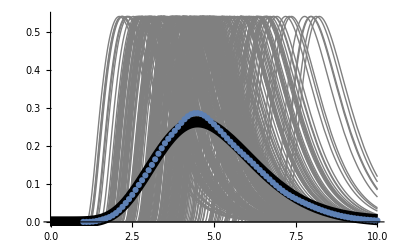

```mathematica
xvals=Range[1,10,0.1];
Show[
Plot[PDF[GammaDistribution[κ, 1/r],x-shift],{x,0,10}, PlotStyle->{Gray,Thin}, PlotRange->All],
Plot[PDF[GammaDistribution[αtotal, 1/r],x],{x,0,10}, PlotStyle->{Black,Thickness[0.02]}],
ListPlot[{
xvals,
Total[Table[PDF[GammaDistribution[κ, 1/r], x-shift],{x,xvals}]ᵀ]/Length[shift]}ᵀ
]]
```